# B → K^* Form Factors Horgan et al. arXiv:1310.3722, lattice - v2 - v3 Horgan et al. arXiv:1501.00367, lattice - v2 Bharucha/Straub/Zwicky, arXiv:1503.05534, LCSR - vNotYet

```mathematica
Quit[]
```

```mathematica
Needs["MultivariateStatistics`"]
```

# Results from arXiv:1310.3722 v2

## Parametrizations for eq(40) with c_01= 0

```mathematica
MB = 5.279;
MKstar = 0.896;
MBsStar = 5.4154;
MBs1 = MB + 0.550;
tPlus = (MB + MKstar)^2;
t0 = 12;
deltaX = 0;
```

```mathematica
z[t_, t0_, tPlus_] := (Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
```

```mathematica
lqcdFFV = Function[{t},1 / (1 - t / MBsStar^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBsStar^2)]

```mathematica
lqcdFFA1 = Function[{t},1 / (1 - t / MBs1^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

```mathematica
lqcdFFA12 = Function[{t},1 / (1 - t / MBs1^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

change this line to calculate desired form factor by setting to lqcdFF{V,A1,A12}

```mathematica
lqcdFF = lqcdFFA12
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

## Distribution in table VI

```mathematica
meansLQCDV = {0.521, -2.00};
covLQCDV = {
{+5.0*10^(-3), +5.6*10^(-2)},
{+5.6*10^(-2), +8.5*10^(-1)}
};
meansLQCDA1 = {0.293,0.16};
covLQCDA1 = {
{+5.8*10^(-4), +6.3*10^(-3)},
{+6.3*10^(-3), +7.8*10^(-2)}
};
meansLQCDA12 = {0.217,0.32};
covLQCDA12 = {
{+7.3*10^(-4), +9.3*10^(-3)},
{+9.3*10^(-3), +1.4*10^(-1)}
};
```

```mathematica
means = meansLQCDA12;
cov = covLQCDA12;
```

```mathematica
ClearAll[f]
f[i_][x_, y_] := lqcdFF[i]//. {a[0] ->  x, a[1] ->  y(*,c[0, 1] -> z*)};
```

```mathematica
dist = MultinormalDistribution[means, cov];
pdf = PDF[dist, {a[0], a[1]}]
```

40.1543 ⅇ^(1/2 (-(-0.217+a[0]) (8911.52 (-0.217+a[0])-591.98 (-0.32+a[1]))-(-591.98 (-0.217+a[0])+46.4672 (-0.32+a[1])) (-0.32+a[1])))

```mathematica
SeedRandom[1253456];
```

```mathematica
parsamples = RandomVariate[dist, 50000];
```

```mathematica
ClearAll[fobservables]
fobservables[x_, y_, z_] := observables //. {a[0] ->  x, a[1] ->  y};
```

2

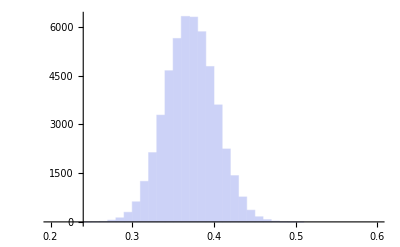

```mathematica
fsamples[i_] := Apply[f[i], parsamples, 1];
samples=Table[fsamples[i], {i, {15,19.21}}];
n=Length[samples]
hist[i_, p_List] := Histogram[samples[[i]], p]
hist[1, {0.2, 0.6, 0.01}]
```

```mathematica
fmean[i_] := Mean[samples[[i]]]
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]]
SetAttributes[fcov, Orderless]
```

```mathematica
fmeanvector = Table[fmean[i], {i, 1, n}]
```

{0.371041,0.440076}

Symmetrize covariance

```mathematica
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
fcovmatrix//MatrixForm
```

(0.000942159 | 0.000171851
0.000171851 | 0.000749573)

```mathematica
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}]
```

{0.0306946,0.0273783}

```mathematica
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}]
fcorrmatrix // MatrixForm
```

{{1.,0.204495},{0.204495,1.}}

(1. | 0.204495
0.204495 | 1.)

```mathematica
dist = MultinormalDistribution[fmeanvector, fcovmatrix];
```

```mathematica
PDF[dist, fmeanvector]
```

193.476

```mathematica
Inverse[fcovmatrix]
Det[fcovmatrix]
```

{{1107.71,-253.96},{-253.96,1392.32}}

6.76684×10^-7

# Results from arXiv:1310.3722 v3

## Numerical input - see tables

```mathematica
mass[Bd]=5.279; (* [GeV] *)
mass[Bs]=5.366; 
mass[Kstar]=0.892;
mass[phi]=1.020;
```

pion decay constant [below eq.(39)]

```mathematica
fPi = 0.132; (* [GeV] *)
```

Δm for pole-masses entering blaschke factor from table V in GeV

```mathematica
Delm[Bd,Kstar,A0]=0.087;
Delm[Bd,Kstar,V|T1]= 0.135;
Delm[Bd,Kstar,A1|A12|T2|T23]=0.550;
Delm[Bs,phi,A0]=0.0;
Delm[Bs,phi,V|T1]= 0.045;
Delm[Bs,phi,A1|A12|T2|T23]=0.440;
Delm[Bs,Kstar,A0]=-0.087;
Delm[Bs,Kstar,V|T1]= -0.042;
Delm[Bs,Kstar,A1|A12|T2|T23]=0.350;
```

mean values, standard deviations and correlation matrices for B→K^*form factors for parameters {a_0,a_1}, see table VII

```mathematica
mean[Bd,Kstar,V]={0.496,-2.03};
std[Bd,Kstar,V]={0.067, 0.92};
cor[Bd, Kstar,V]={{1.0,0.86},{0.86,1.0}};
(* *)
mean[Bd,Kstar,A1]={0.286,0.19};
std[Bd,Kstar,A1]={0.024, 0.28};
cor[Bd, Kstar,A1]={{1.0,0.94},{0.94,1.0}};
(* *)
mean[Bd,Kstar,A12]={0.216,0.32};
std[Bd,Kstar,A12]={0.027, 0.38};
cor[Bd, Kstar,A12]={{1.0,0.91},{0.91,1.0}};
```

```mathematica
cov[B_,V_,FF_]:=Module[
{res},
len= Length[cor[B,V,FF]];
res=Table[cor[B,V,FF][[i,j]] std[B,V,FF][[i]]std[B,V,FF][[j]],{i,len},{j,len}]
]
```

## FF parametrization

Blaschke factor from eq.(38)

```mathematica
blaschke[t_,B_,V_,FF_]:= 1-t/(mass[B] + Delm[B,V,FF])^2
```

variable transformation from q^2→z  eq.(36), t_0= 12 GeV^2[see above eq.(37)]

```mathematica
t0 = 12.;
z[t_,B_,V_] := Module[
{tPlus,res},
tPlus = (mass[B] + mass[V])^2;
res =(Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
]
```

Δx and Δx_s [see below eq.(39)] - not used, set to zero

general form factor parametrization eq.(42) for B→V with B = {B_d, B_s} and V = {K^*,ϕ } !!! not all combinations supported

```mathematica
ff[t_,B_,V_,FF_] := 1/blaschke[t, B,V,FF](a[B,V,FF,0](1.0)+ a[B,V,FF,1] z[t,B,V])
```

constant systematic uncertainty of 5% from table XII

```mathematica
sysffunc = 0.05;
```

```mathematica
q2max[B_,V_]:=(mass[B]-mass[V])^2;
```

## Generate form factors

generate form factor FF for transition B→V 
- at q^2 values in "q2List" 
- with (number of samples)=”Nsamples”
- numerical output with number of “digits”

```mathematica
genFF[B_,V_,FF_,q2List_,Nsamples_,digits_]:= Module[
{dist,pdf,n,parsamples,f,fsamples, samples,fmeanvector,fcov,fcovmatrix,fsigvector,fsigvectorFinal,fcorrmatrix},
(* *)
Print["\nForm factor ",FF," for ", B,"->",V," @ q^2 = ",q2List, " GeV^2"];
dist = MultinormalDistribution[mean[B,V,FF], cov[B,V,FF]];
pdf = PDF[dist, {a[B,V,FF,0], a[B,V,FF,1]}];
n = Length[q2List];
SeedRandom[1253457];
parsamples = RandomVariate[dist, Nsamples];
f[t_][a0_,a1_]:=ff[t,B,V,FF]//. {a[B,V,FF, 0]->a0,a[B,V,FF,1]->a1};
fsamples[t_]:= Apply[f[t], parsamples, 1];
samples=(fsamples[#])&/@ q2List;
fmeanvector= Table[Mean[samples[[i]]],{i, 1, n}];
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]];
SetAttributes[fcov, Orderless];
Print["Central values                         : ",NumberForm[fmeanvector, digits]];
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}];
Print["Standard deviations (no systematics)   : ",NumberForm[fsigvector, digits], " = ",NumberForm[100. fsigvector/fmeanvector, digits]," %"];
fsigvectorFinal = Sqrt[fsigvector^2+ (sysffunc fmeanvector)^2];
Print["Standard deviations (with systematics) : ",NumberForm[fsigvectorFinal, digits], " = ",NumberForm[100. fsigvectorFinal/fmeanvector, digits]," %"];
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}];
Print["Correlation matrix : ", NumberForm[fcorrmatrix,digits-1]];
]
```

some checks with table XXXI - central values ok, standard deviations need inclusion of systematic uncertainties

```mathematica
checkq2List = {0.,12.,16.,q2max[Bd,Kstar]};
(genFF[Bd,Kstar,#,checkq2List, 100000,3])& /@ {V,A1,A12}
```

Form factor V for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.304,0.839,1.28,1.92}

Standard deviations (no systematics)   : {0.149,0.114,0.0865,0.111} = {48.9,13.5,6.77,5.79} %

Standard deviations (with systematics) : {0.15,0.121,0.108,0.147} = {49.1,14.4,8.42,7.65} %

Correlation matrix : {{1.,0.95,0.68,-0.23},{0.95,1.,0.87,0.069},{0.68,0.87,1.,0.56},{-0.23,0.069,0.56,1.}}

Form factor A1 for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.304,0.442,0.525,0.624}

Standard deviations (no systematics)   : {0.0498,0.0372,0.0258,0.0189} = {16.4,8.41,4.91,3.03} %

Standard deviations (with systematics) : {0.052,0.0432,0.0368,0.0365} = {17.1,9.78,7.01,5.85} %

Correlation matrix : {{1.,0.98,0.89,0.14},{0.98,1.,0.96,0.32},{0.89,0.96,1.,0.58},{0.14,0.32,0.58,1.}}

Form factor A12 for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.246,0.334,0.383,0.438}

Standard deviations (no systematics)   : {0.0616,0.0418,0.0269,0.0296} = {25.,12.5,7.02,6.77} %

Standard deviations (with systematics) : {0.0628,0.045,0.033,0.0369} = {25.5,13.5,8.62,8.41} %

Correlation matrix : {{1.,0.97,0.75,-0.33},{0.97,1.,0.89,-0.087},{0.75,0.89,1.,0.38},{-0.33,-0.087,0.38,1.}}

{Null,Null,Null}

generate constraints for EOS

```mathematica
EOSq2List = {15., 19.21};
(genFF[Bd,Kstar,#,EOSq2List, 100000,3])& /@{V,A1,A12}
```

Form factor V for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {1.14,1.91}

Standard deviations (no systematics)   : {0.0926,0.11} = {8.1,5.77} %

Standard deviations (with systematics) : {0.109,0.146} = {9.52,7.63} %

Correlation matrix : {{1.,0.39},{0.39,1.}}

Form factor A1 for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.502,0.623}

Standard deviations (no systematics)   : {0.0291,0.0188} = {5.8,3.03} %

Standard deviations (with systematics) : {0.0384,0.0364} = {7.66,5.84} %

Correlation matrix : {{1.,0.5},{0.5,1.}}

Form factor A12 for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.369,0.437}

Standard deviations (no systematics)   : {0.0307,0.0294} = {8.31,6.72} %

Standard deviations (with systematics) : {0.0358,0.0366} = {9.7,8.37} %

Correlation matrix : {{1.,0.21},{0.21,1.}}

{Null,Null,Null}

# Results from arXiv:1501.00367 v2

Provide now simultaneous fit of 
i = vector) vector FF V and axial-vector FF’s A_(0,1,12)
i = tensor) tensor FF’s T_(1,2,23)

## Numerical Input

meson masses

```mathematica
mass[Bd]=5.279; (* [GeV] *)
mass[Bs]=5.366; 
mass[Kstar]=0.892;
mass[phi]=1.020;
```

pion decay constant [below eq.(39)]

```mathematica
fPi = 0.132; (* [GeV] *)
```

Δm for pole-masses entering blaschke factor from table 4 in GeV

```mathematica
Delm[Bd,Kstar,A0]=0.087;
Delm[Bd,Kstar,V|T1]= 0.135;
Delm[Bd,Kstar,A1|A12|T2|T23]=0.550;
Delm[Bs,phi,A0]=0.0;
Delm[Bs,phi,V|T1]= 0.045;
Delm[Bs,phi,A1|A12|T2|T23]=0.440;
Delm[Bs,Kstar,A0]=-0.087;
Delm[Bs,Kstar,V|T1]= -0.042;
Delm[Bs,Kstar,A1|A12|T2|T23]=0.350;
```

mean values, standard deviations and correlation matrices for
1)  B→K^*FFs of parameters {a_0,a_1}, see ancillary files av_sl_results.d, av_sl_covariance.d

```mathematica
mean[Bd,Kstar,vector]={
0.497528420813,-2.0150648425,0.502302643141,-1.60847600112,
0.284803612469,0.191411584999,0.219527522577,0.332374417965
};
covUpperTriangleMat[Bd, Kstar,vector]={
{0.00444654018992,0.0524970754225,2.37306288148 10^(-20),-2.95976605864 10^(-19),
9.33920040692  10^(-20), 5.44187127382 10^(-19),1.77329950593 10^(-20),-2.19702205261 10^(-19)},
{0.839955459133,1.17941203146  10^(-18),6.43096859783 10^(-18),1.30609221482 10^(-18),
8.89537194192 10^(-18),8.16117124897 10^(-19),4.89571706323 10^(-18)},
{0.00136946827176,0.0110440703514,1.31321639273 10^(-7),-4.09678532204 10^(-7),
0.000794991170373,0.00986195471942},
{0.200005848693,-0.000417726083314,0.0013031622938,0.00965835763816,
0.124472699853},
{0.000543873928258,0.00620191457205,4.02729647337 10^(-6),-0.00034059829966},
{0.078649854783,-1.25637855037 10^(-5),0.00106255002783},
{0.00056438444752,0.00695753530286},
{0.0901066592905}
};
```

see ancillary files t_sl_results.d, t_sl_covariance.d

```mathematica
mean[Bd,Kstar,tensor]={
0.419712711234,-1.36328797303,0.279965680646,
0.11706607999,0.523462757534,-0.27135970224
};
covUpperTriangleMat[Bd, Kstar,tensor]={
{0.000578803972895,0.00311342645125,0.000398503077207,0.00466585264398,6.91175406734 10^(-6),-0.000475345379278},{0.0668607343908,0.00403734128983,0.0511218767784,-2.55954151772 10^(-5),0.00176028577067},
{0.000379492472464,0.00429334278455,1.03047879282 10^(-5),-0.000708696125234},
{0.0558754013656,-6.4761686916 10^(-5),0.00445388657204},
{0.00203658876913,0.0248795682942},
{0.335383041904}
};
```

2)  B_s→ϕ FFs of parameters {a_0,a_1}, see tables 5 and 6

3)  B_s→K^*FFs of parameters {a_0,a_1}, see tables 5 and 6

generate covariance matrices from Upper Triangle matrices

```mathematica
cov[Bq_,VV_,FFtype_]:=Module[
{res,len},
len = Length[covUpperTriangleMat[Bq,VV,FFtype]];
res=DiagonalMatrix[Table[1,{i,len}]];
Do[Do[
k=j-(i-1);
res[[i,j]]=covUpperTriangleMat[Bq,VV,FFtype][[i,k]];
res[[j,i]]=res[[i,j]],
{j,i,len}],{i,len}
];
res=res
]
```

```mathematica
corr[Bq_,VV_,FFtype_]:=Module[
{len,cova},
cova=cov[Bq,VV,FFtype];
len=Length[cova];
Table[cova[[i,j]]/Sqrt[cova[[i,i]] cova[[j,j]]], {i,len},{j,len}]
];
```

1)  Results for B→K^*FFs

```mathematica
cov[Bd,Kstar,vector] //MatrixForm
```

(0.00444654 | 0.0524971 | 2.37306×10^-20 | -2.95977×10^-19 | 9.3392×10^-20 | 5.44187×10^-19 | 1.7733×10^-20 | -2.19702×10^-19
0.0524971 | 0.839955 | 1.17941×10^-18 | 6.43097×10^-18 | 1.30609×10^-18 | 8.89537×10^-18 | 8.16117×10^-19 | 4.89572×10^-18
2.37306×10^-20 | 1.17941×10^-18 | 0.00136947 | 0.0110441 | 1.31322×10^-7 | -4.09679×10^-7 | 0.000794991 | 0.00986195
-2.95977×10^-19 | 6.43097×10^-18 | 0.0110441 | 0.200006 | -0.000417726 | 0.00130316 | 0.00965836 | 0.124473
9.3392×10^-20 | 1.30609×10^-18 | 1.31322×10^-7 | -0.000417726 | 0.000543874 | 0.00620191 | 4.0273×10^-6 | -0.000340598
5.44187×10^-19 | 8.89537×10^-18 | -4.09679×10^-7 | 0.00130316 | 0.00620191 | 0.0786499 | -0.0000125638 | 0.00106255
1.7733×10^-20 | 8.16117×10^-19 | 0.000794991 | 0.00965836 | 4.0273×10^-6 | -0.0000125638 | 0.000564384 | 0.00695754
-2.19702×10^-19 | 4.89572×10^-18 | 0.00986195 | 0.124473 | -0.000340598 | 0.00106255 | 0.00695754 | 0.0901067)

```mathematica
corr[Bd,Kstar,vector] //MatrixForm
```

(1. | 0.859005 | 9.61661×10^-18 | -9.92487×10^-18 | 6.0055×10^-17 | 2.90997×10^-17 | 1.1194×10^-17 | -1.0976×10^-17
0.859005 | 1. | 3.47745×10^-17 | 1.56901×10^-17 | 6.11078×10^-17 | 3.46088×10^-17 | 3.74832×10^-17 | 1.77955×10^-17
9.61661×10^-18 | 3.47745×10^-17 | 1. | 0.667316 | 0.000152164 | -0.0000394746 | 0.904271 | 0.887787
-9.92487×10^-18 | 1.56901×10^-17 | 0.667316 | 1. | -0.0400517 | 0.0103903 | 0.909064 | 0.927202
6.0055×10^-17 | 6.11078×10^-17 | 0.000152164 | -0.0400517 | 1. | 0.948261 | 0.00726904 | -0.0486536
2.90997×10^-17 | 3.46088×10^-17 | -0.0000394746 | 0.0103903 | 0.948261 | 1. | -0.00188575 | 0.0126218
1.1194×10^-17 | 3.74832×10^-17 | 0.904271 | 0.909064 | 0.00726904 | -0.00188575 | 1. | 0.97564
-1.0976×10^-17 | 1.77955×10^-17 | 0.887787 | 0.927202 | -0.0486536 | 0.0126218 | 0.97564 | 1.)

```mathematica
cov[Bd,Kstar,tensor] //MatrixForm
```

(0.000578804 | 0.00311343 | 0.000398503 | 0.00466585 | 6.91175×10^-6 | -0.000475345
0.00311343 | 0.0668607 | 0.00403734 | 0.0511219 | -0.0000255954 | 0.00176029
0.000398503 | 0.00403734 | 0.000379492 | 0.00429334 | 0.0000103048 | -0.000708696
0.00466585 | 0.0511219 | 0.00429334 | 0.0558754 | -0.0000647617 | 0.00445389
6.91175×10^-6 | -0.0000255954 | 0.0000103048 | -0.0000647617 | 0.00203659 | 0.0248796
-0.000475345 | 0.00176029 | -0.000708696 | 0.00445389 | 0.0248796 | 0.335383)

```mathematica
corr[Bd,Kstar,tensor] //MatrixForm
```

(1. | 0.500481 | 0.850285 | 0.820455 | 0.00636606 | -0.0341172
0.500481 | 1. | 0.801509 | 0.836394 | -0.00219344 | 0.0117551
0.850285 | 0.801509 | 1. | 0.93236 | 0.0117216 | -0.0628186
0.820455 | 0.836394 | 0.93236 | 1. | -0.00607094 | 0.0325356
0.00636606 | -0.00219344 | 0.0117216 | -0.00607094 | 1. | 0.951964
-0.0341172 | 0.0117551 | -0.0628186 | 0.0325356 | 0.951964 | 1.)

2)  Results for B_s→ϕ  FFs
3)  Results for B_s→K^*  FFs

## FF parameterization - eq-numbers refer to arXiv:1310.3722

Blaschke factor from eq.(38)

```mathematica
blaschke[t_,Bq_,VV_,FF_]:=
 1-t/(mass[Bq] + Delm[Bq,VV,FF])^2
```

variable transformation from q^2→z  eq.(36), t_0= 12 GeV^2[see above eq.(37)]

```mathematica
t0 = 12.;
z[t_,Bq_,VV_] := Module[
{tPlus,res},
tPlus = (mass[Bq] + mass[VV])^2;
res =(Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
]
```

Δx and Δx_s [see below eq.(39)] - not used, set to zero

general form factor parametrization eq.(42) for B→V with B = {B_d, B_s} and V = {K^*,ϕ } !!! not all combinations supported

```mathematica
ff[t_,Bq_,VV_,FF_]:=
1/blaschke[t, Bq,VV,FF](a[Bq,VV,FF,0](1.0)+ a[Bq,VV,FF,1] z[t,Bq,VV])
```

constant systematic uncertainty of 5% from table XII

```mathematica
sysffunc = 0.05;
```

```mathematica
q2max[Bq_,VV_]:=(mass[Bq]-mass[VV])^2;
```

## Generate form factors

generate FF’s ={FF_1, ... FF_N} for transitions: B_q → V

- at q^2 values in "q2List = {q_1^2, ... q_M^2}"
- with (number of samples)=”Nsamples”
- numerical output with number of “digits”
- test whether covariance matrix positive definite and invertable, otherwise correlation can not be used in EOS

outputs are

1) mean value
2) standard deviation
    a) without systematic uncertainty
    b) with systematic ⟸ this one should be used
3) correlation matrix 

for 

  {FF_1(q_1^2),FF_2(q_1^2)...FF_N(q_1^2),   ...   FF_1(q_M^2),FF_2(q_M^2)...FF_N(q_M^2)}

```mathematica
genFF[Bq_,VV_,FFtype_,q2List_,Nsamples_,digits_]:= Module[
{dist,parsamples,f, samples,fmeanvector,fcov,fcovmatrix,fsigvector,fsigvectorFinal,fcorrmatrix},
(* *)
Print["\nFF's ",FFtype," for ", Bq,"->",VV," @ q^2 = ",q2List, " GeV^2"];
f[vector][Va0_,Va1_,A0a0_,A0a1_,A1a0_,A1a1_,A12a0_,A12a1_]:=Module[
{res},
res ={
ff[#,Bq,VV,V]//. {a[Bq,VV,V, 0]->Va0,a[Bq,VV,V,1]->Va1},
ff[#,Bq,VV,A0]//. {a[Bq,VV,A0, 0]->A0a0,a[Bq,VV,A0,1]->A0a1},
ff[#,Bq,VV,A1]//. {a[Bq,VV,A1, 0]->A1a0,a[Bq,VV,A1,1]->A1a1},
ff[#,Bq,VV,A12]//. {a[Bq,VV,A12, 0]->A12a0,a[Bq,VV,A12,1]->A12a1}
}&/@ q2List;
res = Join@@res
];
f[tensor][T1a0_,T1a1_,T2a0_,T2a1_,T23a0_,T23a1_]:=Module[
{res},
res={
ff[#,Bq,VV,T1]//. {a[Bq,VV,T1, 0]->T1a0,a[Bq,VV,T1,1]->T1a1},
ff[#,Bq,VV,T2]//. {a[Bq,VV,T2, 0]->T2a0,a[Bq,VV,T2,1]->T2a1},
ff[#,Bq,VV,T23]//. {a[Bq,VV,T23, 0]->T23a0,a[Bq,VV,T23,1]->T23a1}
}&/@q2List;
res=Join@@res
];
Switch[FFtype,
vector,n=4 Length[q2List],
tensor,n=3 Length[q2List]
];
dist = MultinormalDistribution[mean[Bq,VV,FFtype], cov[Bq,VV,FFtype]];
SeedRandom[1253457];
parsamples = RandomVariate[dist, Nsamples];
samples= Apply[f[FFtype], parsamples, 1];
samples=Transpose[samples];
fmeanvector= Table[Mean[samples[[i]]],{i, 1, n}];
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]];
SetAttributes[fcov, Orderless];
Print["Central values                         : ",NumberForm[fmeanvector, digits]];
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
(* enforce symmetric covariance matrix *)
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
Print["\nDet[fcovmatrix] = ",Det[fcovmatrix]];
Print["\nInverse covariance = ",Inverse[fcovmatrix]];
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}];
Print["Standard deviations (no systematics)   : ",NumberForm[fsigvector, digits],
"\n                                       = ",NumberForm[100. fsigvector/fmeanvector, digits]," %"];
fsigvectorFinal = Sqrt[fsigvector^2+ (sysffunc fmeanvector)^2];
Print["Standard deviations (with systematics) : ",NumberForm[fsigvectorFinal, digits],
"\n                                       = ",NumberForm[100. fsigvectorFinal/fmeanvector, digits]," %"];
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}];
Print["Correlation matrix : ", MatrixForm[NumberForm[fcorrmatrix,digits-1]]];
]
```

checks with table 11 - central values and standard deviations need inclusion of systematic uncertainties -> agree very well

```mathematica
checkq2List = {0.,12.,16.,q2max[Bd,Kstar]};
(genFF[Bd,Kstar,#,checkq2List, 50000,3])& /@ {vector, tensor}
```

FF's vector for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.306,0.351,0.303,0.251,0.841,0.861,0.44,0.34,1.28,1.28,0.523,0.389,1.92,1.91,0.621,0.444}

Det[fcovmatrix] = 8.12721×10^-174

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0217409, 0.0000928859, 0.0000311284, 0.0000665385, 0.0158466, 0.0000946571, 0.0000185002, 0.0000447707, 0.00858719, 0.0000868634, 6.64813×10^-6, 0.0000234159, -0.00377462, 0.0000687102, -0.0000104339, -7.79796×10^-6}, « 14 », {-7.79796×10^-6, -0.0001168, 0.000052033, -0.0000835798, -6.73006×10^-6, -0.0000274588, 0.000112597, -« 23 », -« 22 », 0.000063966, 0.000154982, 0.0000600135, -1.99393×10^-6, 0.000213254, 0.000209259, 0.000150707}} may contain significant numerical errors.

Inverse covariance = {{-2.41881×10^17,-2.08371×10^14,5.21596×10^16,2.05268×10^16,1.38748×10^17,1.42312×10^16,-7.49762×10^16,-5.89387×10^16,2.68238×10^17,-2.18222×10^16,3.41112×10^15,5.0714×10^16,-2.00444×10^17,8.26394×10^15,2.4847×10^16,-1.09504×10^16},{2.24462×10^15,-8.41965×10^16,-2.06453×10^16,-3.94338×10^17,3.08635×10^15,2.49348×10^16,1.13442×10^15,4.38157×10^17,-9.38618×10^15,1.26912×10^17,4.65273×10^16,1.90065×10^17,4.53216×10^15,-8.09715×10^16,-2.99361×10^16,-2.78475×10^17},{4.99198×10^16,-3.16871×10^16,-2.03902×10^18,-1.38466×10^17,2.54856×10^16,-9.82608×10^16,3.39363×10^18,2.53634×10^17,-1.40699×10^17,2.15931×10^17,-9.0945×10^17,-1.0064×10^17,7.44309×10^16,-9.47764×10^16,-6.45468×10^17,-2.75085×10^16},{-4.13186×10^15,-3.34302×10^17,1.93581×10^16,-3.69843×10^17,2.0318×10^16,-1.94315×10^17,-1.12728×10^17,9.94419×10^17,-2.37188×10^16,9.62137×10^17,1.43683×10^17,-8.00493×10^17,7.54051×10^15,-4.96714×10^17,-5.05726×10^16,1.49753×10^17},{1.5175×10^17,-4.84486×10^14,4.26009×10^15,1.33924×10^16,-2.71116×10^17,1.34289×10^16,-3.29829×10^16,-3.11334×10^16,1.21963×10^17,-2.00248×10^16,4.53334×10^16,2.08082×10^16,1.33036×10^16,7.47026×10^15,-1.6887×10^16,-1.98896×10^15},{-1.32513×10^15,1.50845×10^17,7.90652×10^15,8.30566×10^16,1.18859×10^16,-2.93175×10^17,1.02573×10^17,5.3407×10^17,-1.6074×10^16,1.60849×10^17,-1.90608×10^17,-1.09071×10^18,5.69872×10^15,-3.37883×10^15,8.40103×10^16,4.9978×10^17},{-5.42547×10^16,-2.50752×10^15,2.86378×10^18,2.27036×10^17,-6.56947×10^16,3.18219×10^17,-6.24291×10^18,-5.01342×10^17,2.12831×10^17,-4.92196×10^17,3.75419×10^18,3.08387×10^17,-1.04107×10^17,1.87237×10^17,-1.33366×10^17,-1.50913×10^16},{3.01146×10^15,3.95803×10^17,-1.05084×10^17,1.07295×10^18,-5.12535×10^16,1.00115×10^18,2.91832×10^17,-2.37429×10^18,7.47552×10^16,-2.34377×10^18,-2.43022×10^17,1.46577×10^18,-2.77605×10^16,1.04871×10^18,4.90894×10^16,-7.48308×10^16},{2.47736×10^17,1.18351×10^15,-1.1174×10^17,-6.24482×10^16,1.48141×10^17,-4.98295×10^16,2.02972×10^17,1.67764×10^17,-7.32407×10^17,7.55145×10^16,-7.8352×10^16,-1.34923×10^17,3.82612×10^17,-2.84187×10^16,-2.34007×10^16,2.51848×10^16},{-2.35169×10^15,-6.97908×10^16,2.83191×10^16,6.47086×10^17,-2.46487×10^16,4.08891×10^17,-1.62479×10^17,-1.69751×10^18,4.36023×10^16,-5.01301×10^17,2.06118×10^17,1.32953×10^18,-1.78311×10^16,1.64791×10^17,-7.22711×10^16,-2.32187×10^17},{-2.60937×10^16,7.85385×10^16,-2.06581×10^16,-5.60222×10^16,5.04145×10^16,-3.03291×10^17,2.51126×10^18,2.45992×10^17,-2.69568×10^16,3.19096×10^17,-4.16403×10^18,-2.81219×10^17,3.11804×10^13,-9.17501×10^16,1.73787×10^18,8.98447×10^16},{4.64106×10^15,1.20275×10^17,1.30862×10^17,-9.32226×10^17,3.83124×10^16,-1.22354×10^18,-2.25092×10^17,1.65×10^18,-6.97574×10^16,1.67454×10^18,7.06001×10^16,-5.80937×10^17,2.88778×10^16,-5.93953×10^17,3.62897×10^16,-2.25769×10^17},{-1.92501×10^17,-5.41673×10^14,6.4105×10^16,3.23852×10^16,-2.02665×10^15,2.49842×10^16,-1.08556×10^17,-8.85157×10^16,3.90793×10^17,-3.79644×10^16,3.17168×10^16,7.25099×10^16,-2.2822×10^17,1.43079×10^16,1.89811×10^16,-1.4127×10^16},{1.76415×10^15,-5.75767×10^15,-1.87838×10^16,-3.99381×10^17,1.06143×10^16,-1.46741×10^17,6.2565×10^16,8.17921×10^17,-2.02892×10^16,2.40588×10^17,-6.08855×10^16,-4.35137×10^17,8.56455×10^15,-9.42131×10^16,1.60991×10^16,-1.85239×10^16},{3.61061×10^16,-4.89391×10^16,-1.01863×10^18,-4.62413×10^16,-8.3264×10^15,7.78312×10^16,6.5543×10^17,2.45066×10^16,-5.95694×10^16,-2.5182×10^16,1.29007×10^18,6.73654×10^16,3.74868×10^16,-9.22903×10^15,-1.05485×10^18,-5.15808×10^16},{-4.03028×10^15,-2.18926×10^17,-4.51896×10^16,2.05061×10^17,-5.84887×10^15,4.15806×10^17,3.77106×10^16,-1.91743×10^17,1.73376×10^16,-2.18311×10^17,4.27493×10^16,-1.59399×10^17,-8.32532×10^15,-8.83434×10^14,-4.07158×10^16,1.70238×10^17}}

Standard deviations (no systematics)   : {0.147,0.0724,0.049,0.0518,0.113,0.0635,0.036,0.0367,0.0863,0.0635,0.0242,0.0224,0.112,0.0903,0.0171,0.0123}
                                       = {48.1,20.6,16.2,20.6,13.4,7.37,8.17,10.8,6.75,4.96,4.62,5.77,5.81,4.73,2.75,2.76} %

Standard deviations (with systematics) : {0.148,0.0745,0.0513,0.0533,0.12,0.0767,0.0422,0.0405,0.107,0.0902,0.0356,0.0297,0.147,0.131,0.0354,0.0254}
                                       = {48.4,21.2,16.9,21.2,14.3,8.9,9.58,11.9,8.4,7.04,6.8,7.64,7.66,6.88,5.71,5.71} %

Correlation matrix : {{1.,0.0087,0.0043,0.0087,0.95,0.01,0.0035,0.0083,0.67,0.0093,0.0019,0.0071,-0.23,0.0052,-0.0041,-0.0043},{0.0087,1.,-0.013,1.,0.0054,0.9,-0.029,0.99,-0.0011,0.57,-0.055,0.94,-0.011,-0.011,-0.099,-0.13},{0.0043,-0.013,1.,-0.013,0.0011,-0.0006,0.99,-0.0024,-0.0044,0.013,0.89,0.018,-0.011,0.025,0.064,0.086},{0.0087,1.,-0.013,1.,0.0055,0.9,-0.029,0.99,-0.0011,0.57,-0.055,0.94,-0.011,-0.011,-0.099,-0.13},{0.95,0.0054,0.0011,0.0055,1.,0.0066,0.00027,0.0049,0.87,0.0063,-0.0012,0.0037,0.075,0.0038,-0.0047,-0.0049},{0.01,0.9,-0.0006,0.9,0.0066,1.,-0.0016,0.9,-0.00064,0.87,-0.0031,0.87,-0.012,0.42,-0.0057,-0.035},{0.0035,-0.029,0.99,-0.029,0.00027,-0.0016,1.,0.0012,-0.0051,0.03,0.96,0.06,-0.011,0.057,0.23,0.25},{0.0083,0.99,-0.0024,0.99,0.0049,0.9,0.0012,1.,-0.0017,0.58,0.0072,0.97,-0.011,0.012,0.021,-0.012},{0.67,-0.0011,-0.0044,-0.0011,0.87,-0.00064,-0.0051,-0.0017,1.,0.000031,-0.006,-0.0027,0.56,0.00081,-0.0047,-0.0048},{0.0093,0.57,0.013,0.57,0.0063,0.87,0.03,0.58,0.000031,1.,0.057,0.59,-0.01,0.82,0.1,0.082},{0.0019,-0.055,0.89,-0.055,-0.0012,-0.0031,0.96,0.0072,-0.006,0.057,1.,0.13,-0.01,0.11,0.5,0.52},{0.0071,0.94,0.018,0.94,0.0037,0.87,0.06,0.97,-0.0027,0.59,0.13,1.,-0.011,0.056,0.25,0.22},{-0.23,-0.011,-0.011,-0.011,0.075,-0.012,-0.011,-0.011,0.56,-0.01,-0.01,-0.011,1.,-0.0047,-0.0016,-0.0015},{0.0052,-0.011,0.025,-0.011,0.0038,0.42,0.057,0.012,0.00081,0.82,0.11,0.056,-0.0047,1.,0.19,0.19},{-0.0041,-0.099,0.064,-0.099,-0.0047,-0.0057,0.23,0.021,-0.0047,0.1,0.5,0.25,-0.0016,0.19,1.,1.},{-0.0043,-0.13,0.086,-0.13,-0.0049,-0.035,0.25,-0.012,-0.0048,0.082,0.52,0.22,-0.0015,0.19,1.,1.}}

FF's tensor for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.291,0.291,0.498,0.71,0.433,0.809,1.05,0.52,1.01,1.54,0.624,1.26}

Det[fcovmatrix] = 7.5222×10^-133

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00175618, 0.00167311, -5.32868×10^-6, 0.00146972, 0.0012057, 0.0000243758, 0.00104907, 0.00072961, 0.000047379, 0.000302005, 0.0000258127, 0.000078236}, « 10 », {0.000078236, 0.0000721421, -0.000455852, 0.000184367, 0.000247843, 0.0000713294, 0.000269528, 0.000376463, 0.000505525, 0.000393897, 0.000544746, 0.00110278}} may contain significant numerical errors.

Inverse covariance = {{-3.57607×10^17,-8.58149×10^17,-4.16693×10^16,1.79052×10^17,1.66891×10^18,-7.48305×10^16,4.37697×10^17,-7.86427×10^17,2.23273×10^17,-3.12277×10^17,-1.02172×10^17,-1.14735×10^17},{-6.23835×10^17,7.62594×10^17,-2.1632×10^16,1.54162×10^17,-1.76699×10^17,8.28136×10^16,1.01299×10^18,-1.49251×10^18,-8.81701×10^16,-6.41398×10^17,1.01084×10^18,2.61196×10^16},{-5.77978×10^15,-4.98576×10^15,-4.16908×10^17,-3.40883×10^16,1.54108×10^17,-1.02253×10^17,6.53894×10^16,-2.46812×10^17,1.14951×10^18,-2.764×10^16,1.01112×10^17,-6.92672×10^17},{3.34205×10^17,4.29826×10^17,6.19813×10^16,-1.75611×10^18,-1.3544×10^17,7.77583×10^16,2.09619×10^18,-7.81103×10^17,-2.75832×10^17,-6.78758×10^17,5.44503×10^17,1.47036×10^17},{1.52635×10^18,-7.72904×10^17,-3.95682×10^16,1.52412×10^17,1.06396×10^18,-1.03804×10^17,-3.31359×10^18,2.8369×10^16,2.66945×10^17,1.89286×10^18,-4.01317×10^17,-1.32013×10^17},{2.79002×10^15,6.46767×10^16,7.25913×10^16,-6.40761×10^16,1.3796×10^17,-7.45904×10^17,9.54205×10^16,-3.8314×10^17,1.08092×10^18,-3.58551×10^16,1.93447×10^17,-4.17254×10^17},{1.93046×10^17,1.05009×10^18,-1.38345×10^16,2.40859×10^18,-3.14674×10^18,2.80568×10^16,-4.18667×10^18,2.81513×10^18,-1.46104×10^16,1.69906×10^18,-6.52876×10^17,-8.35932×10^14},{-1.09695×10^18,-4.92407×10^17,1.17118×10^17,-6.173×10^17,-1.37022×10^18,-2.01405×10^16,3.18207×10^18,3.45357×10^18,-2.40954×10^17,-1.67055×10^18,-1.69807×10^18,1.60171×10^17},{8.87822×10^15,-9.67956×10^16,8.56223×10^17,1.87449×10^17,-5.9293×10^17,1.49108×10^18,-3.13454×10^17,1.22167×10^18,-4.50974×10^18,1.24983×10^17,-5.61687×10^17,2.3248×10^18},{-2.17493×10^17,-7.49275×10^17,-1.12681×10^16,-8.61702×10^17,1.8851×10^18,-4.07308×10^16,1.79669×10^18,-1.40448×10^18,9.47565×10^16,-7.82874×10^17,2.1217×10^17,-4.54607×10^16},{1.46254×10^17,5.90949×10^17,-6.00709×10^16,3.36844×10^17,4.86265×10^17,5.01793×10^16,-8.2563×10^17,-2.20194×10^18,5.67427×10^16,3.78233×10^17,1.22222×10^18,-5.40885×10^16},{-6.63951×10^15,3.81278×10^16,-5.69533×10^17,-9.5875×10^16,3.26586×10^17,-6.77548×10^17,1.64549×10^17,-6.37269×10^17,2.47257×10^18,-6.63999×10^16,2.86768×10^17,-1.32505×10^18}}

Standard deviations (no systematics)   : {0.0419,0.0411,0.0983,0.0407,0.0302,0.0696,0.046,0.0207,0.0442,0.0663,0.0164,0.0332}
                                       = {14.4,14.1,19.7,5.73,6.97,8.6,4.39,3.98,4.37,4.29,2.63,2.64} %

Standard deviations (with systematics) : {0.0444,0.0436,0.101,0.054,0.0371,0.0805,0.0697,0.0332,0.0671,0.102,0.0352,0.0711}
                                       = {15.3,15.,20.3,7.6,8.58,9.95,6.65,6.39,6.64,6.59,5.65,5.65} %

Correlation matrix : {{1.,0.97,-0.0013,0.86,0.95,0.0084,0.54,0.84,0.026,0.11,0.038,0.056},{0.97,1.,-0.003,0.85,0.98,0.0061,0.54,0.86,0.022,0.12,0.034,0.053},{-0.0013,-0.003,1.,-0.016,-0.026,0.99,-0.026,-0.062,0.88,-0.03,-0.12,-0.14},{0.86,0.85,-0.016,1.,0.85,0.0068,0.89,0.78,0.049,0.6,0.12,0.14},{0.95,0.98,-0.026,0.85,1.,0.016,0.56,0.95,0.093,0.15,0.23,0.25},{0.0084,0.0061,0.99,0.0068,0.016,1.,0.0039,0.032,0.95,0.00019,0.054,0.031},{0.54,0.54,-0.026,0.89,0.56,0.0039,1.,0.54,0.059,0.89,0.17,0.18},{0.84,0.86,-0.062,0.78,0.95,0.032,0.54,1.,0.2,0.19,0.53,0.55},{0.026,0.022,0.88,0.049,0.093,0.95,0.059,0.2,1.,0.057,0.37,0.34},{0.11,0.12,-0.03,0.6,0.15,0.00019,0.89,0.19,0.057,1.,0.18,0.18},{0.038,0.034,-0.12,0.12,0.23,0.054,0.17,0.53,0.37,0.18,1.,1.},{0.056,0.053,-0.14,0.14,0.25,0.031,0.18,0.55,0.34,0.18,1.,1.}}

{Null,Null}

generate constraints for EOS
!!! covariance matrix will be only positive definite for q^2= {15, 19.21} GeV^2 - choosing narrower interval or three points does not work

```mathematica
EOSq2List = {15.,19.21};
(genFF[Bd,Kstar,#,EOSq2List, 100000,6])& /@{vector, tensor}
```

FF's vector for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {1.14464,1.15119,0.49946,0.37489,1.91508,1.89931,0.619687,0.443332}

Det[fcovmatrix] = 2.25842×10^-31

Inverse covariance = {{139.186,-316.594,-0.734008,515.867,-45.6437,157.034,-107.903,-134.397},{-316.594,2.04936×10^7,118.134,-3.33937×10^7,-95.985,-1.01565×10^7,38033.4,1.84814×10^7},{-0.734008,118.134,1670.11,-322.053,-1.18288,-57.0705,28401.4,-41081.2},{515.867,-3.33937×10^7,-322.053,5.44156×10^7,155.904,1.65498×10^7,-103307.,-3.00577×10^7},{-45.6437,-95.985,-1.18288,155.904,97.0768,47.3899,116.196,-248.127},{157.034,-1.01565×10^7,-57.0705,1.65498×10^7,47.3899,5.03368×10^6,-18801.8,-9.15959×10^6},{-107.903,38033.4,28401.4,-103307.,116.196,-18801.8,9.6953×10^6,-1.35109×10^7},{-134.397,1.84814×10^7,-41081.2,-3.00577×10^7,-248.127,-9.15959×10^6,-1.35109×10^7,3.55993×10^7}}

Standard deviations (no systematics)   : {0.0921677,0.0618387,0.0277005,0.0266435,0.110361,0.0898203,0.0171859,0.0123107}
                                       = {8.0521,5.37174,5.54609,7.10701,5.76275,4.72911,2.77332,2.77685} %

Standard deviations (with systematics) : {0.108491,0.0844814,0.0372957,0.0325766,0.146111,0.130714,0.0354314,0.0253557}
                                       = {9.47821,7.33863,7.4672,8.68963,7.6295,6.88219,5.71763,5.71934} %

Correlation matrix : {{1.,0.00052981,0.0021485,0.0010579,0.39269,-0.00047199,-0.00053295,-0.00055847},{0.00052981,1.,0.031735,0.70766,0.0013494,0.71678,0.0757,0.071136},{0.0021485,0.031735,1.,0.070338,0.0044106,0.08122,0.4188,0.42273},{0.0010579,0.70766,0.070338,1.,0.000593,0.046446,0.16102,0.15462},{0.39269,0.0013494,0.0044106,0.000593,1.,0.001416,0.00050542,0.00057568},{-0.00047199,0.71678,0.08122,0.046446,0.001416,1.,0.19819,0.19814},{-0.00053295,0.0757,0.4188,0.16102,0.00050542,0.19819,1.,0.9998},{-0.00055847,0.071136,0.42273,0.15462,0.00057568,0.19814,0.9998,1.}}

FF's tensor for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.944705,0.494866,0.952108,1.53683,0.622428,1.25483}

Det[fcovmatrix] = 2.23591×10^-24

Inverse covariance = {{29560.6,-33599.1,-9.50455,-14741.9,28559.5,-5063.29},{-33599.1,41161.7,-331.865,16660.3,195597.,-108028.},{-9.50455,-331.865,566.573,3.77149,-113699.,56253.4},{-14741.9,16660.3,3.77149,7595.96,-14631.6,2658.92},{28559.5,195597.,-113699.,-14631.6,7.58273×10^7,-3.76041×10^7},{-5063.29,-108028.,56253.4,2658.92,-3.76041×10^7,1.86526×10^7}}

Standard deviations (no systematics)   : {0.0435124,0.02334,0.0516476,0.0656154,0.0163629,0.0330106}
                                       = {4.60593,4.71643,5.42455,4.26954,2.62889,2.63069} %

Standard deviations (with systematics) : {0.0642223,0.0340145,0.0702407,0.101044,0.0351609,0.0708956}
                                       = {6.79813,6.87348,7.37738,6.57488,5.64899,5.64983} %

Correlation matrix : {{1.,0.65399,0.041249,0.82578,0.16258,0.16507},{0.65399,1.,0.10027,0.1903,0.42549,0.429},{0.041249,0.10027,1.,0.046927,0.23557,0.23111},{0.82578,0.1903,0.046927,1.,0.18144,0.18189},{0.16258,0.42549,0.23557,0.18144,1.,0.99996},{0.16507,0.429,0.23111,0.18189,0.99996,1.}}

{Null,Null}

# LCSR results BSZ arXiv:1503.05534

- reads LCSR results from data file <fname> assuming format given by David Straub :

  {
    {q_1^2, q_2^2, ...  q_N^2},
    {
     {mean(A_0(q_1^2)), mean(A_0(q_2^2)), ..., mean(A_0(q_N^2)), 
      mean(A_1(q_1^2)),  mean(A_1(q_2^2)), ..., mean(A_1(q_N^2)),
      mean(A_2(q_2^2)), ...
      mean(V(q_2^2)), ...
      mean(T_1(q_2^2)), ...
      mean(T_2(q_2^2)), ...
      mean(T_3(q_2^2)), ... },
     {unc( as in mean ) ... },
     {{corrlation-matrix }, ..., {}}
    }
  }
  
- remove rows and columns of not-needed form factors specified in <indL>
- stores results of mean values, uncertainties and correlation and covariance matrix in <mean[tag], unc[tag], corr[tag], cov[tag]>
- checks invertability of covariance matrix

```mathematica
Clear[mean,unc,corr,cov];
```

```mathematica
LCSRresults[fname_, indL_,tag_]:=Module[
{res,len,q2List},
res=ReadList[FileNameJoin[{NotebookDirectory[],fname}]];
len=Length[indL];
Print["  Using tag = ",tag];
Print["  Dimension of input = ",Length[res[[1,2,1]] ]];
Print["  Dimension of index list = ",len];
q2List=res[[1,1]];
Print["  Form factors at q^2 values : ",q2List];
mean[tag] =res[[1,2,1,#]]&/@indL;
unc[tag]=res[[1,2,2,#]]&/@indL;
corr[tag]=res[[1,2,3,#]]&/@indL;
corr[tag]=(Transpose[corr[tag]])[[#]]&/@ indL;
Print["  Mean values          : \n\n",Table[FortranForm[mean[tag][[i]]],{i,len}]];
Print["\n  Uncertainties values : \n\n",Table[FortranForm[unc[tag][[i]]],{i,len}]];
Print["\n  Correlation matrix   : \n\n",Table[FortranForm[corr[tag][[i,j]]],{i,len},{j,len}]];
cov[tag]=Table[corr[tag][[i,j]] unc[tag][[i]] unc[tag][[j]], {i,len},{j,len}];
Print["\n  Det[cov] = ",Det[cov[tag]]];
Inverse[cov[tag]];
];
```

Results v1

```mathematica
LCSRresults["InputData_BtoKstar_LCSR_StandardBasis.dat",Table[i, {i,16}],v1];
```

Using tag = v1

Dimension of index list = 16

Form factors at q^2 values : {0.1,2.1,4.1,6.1}

Mean values          : 

{0.3931360084310848,0.44039370875906125,0.49687830852199616,0.5653422377269293,0.28960640973145696,0.3038996582693178,0.3198466660096681,0.33786144803732643,0.24856939107445855,0.27271823671650736,0.3006774595083485,0.3334309248540632,0.3673120680346128,0.4112494585119839,0.4638122643080778,0.5275947645824033}

Uncertainties values : 

{0.03550007563641091,0.037943215466950425,0.04091393460653374,0.04472778481964711,0.027007201269037082,0.02712550657063787,0.027346431873910445,0.027763634334125178,0.04253285457836853,0.04644523426854137,0.0513413656680612,0.05776989540861154,0.03567682653724426,0.03822650159193756,0.04127909235116033,0.045105277447151315}

Correlation matrix   : 

{{1.0000000000000004,0.9962225522158096,0.9819195025692343,0.9515776774515233,-0.1300729499782839,-0.12236045286025571,-0.11348632881564459,-0.10340229472073176,-0.455739633291322,-0.4673406088532873,-0.4793425155127851,-0.490943664332569,-0.07256555612638607,-0.05766171877326252,-0.04052847947689741,-0.02108513160553963},{0.9962225522158096,1.,0.9946447666924765,0.9746482590157562,-0.11287446090241274,-0.10226273726725213,-0.0902257680860569,-0.07680820801491778,-0.4388922213101618,-0.4504854997182176,-0.46299264811737456,-0.4758264859659691,-0.04764671576575598,-0.02886743451482557,-0.007468949400513591,0.016503918318901474},{0.9819195025692343,0.9946447666924765,0.9999999999999997,0.9925455984882545,-0.09156693084489684,-0.07758188482292058,-0.061863490604838534,-0.04456371534652456,-0.4147546363314176,-0.4262134131805498,-0.4391880672826303,-0.4533554767410729,-0.017670953280121263,0.005604443964096819,0.03195584538887368,0.06119470179408488},{0.9515776774515233,0.9746482590157562,0.9925455984882545,1.,-0.06530107386773912,-0.04749120073020017,-0.027597920675008616,-0.0058942045893700425,-0.38068981899003723,-0.39181312781426747,-0.40513937010974327,-0.4206649819257092,0.017911629525356333,0.04627008604527669,0.07822782737360687,0.11343696320480515},{-0.1300729499782839,-0.11287446090241274,-0.09156693084489684,-0.06530107386773912,0.9999999999999997,0.9971018729623589,0.9863515583415491,0.964098294106404,0.9416713389111339,0.9352087170882717,0.922844135351268,0.9021626621547396,0.905022016254851,0.8985455541242857,0.8839689614220189,0.8574513826969588},{-0.12236045286025571,-0.10226273726725213,-0.07758188482292058,-0.04749120073020017,0.9971018729623589,0.9999999999999996,0.996016218883038,0.9814822663575691,0.9364655903102275,0.9339685993282945,0.9260799262978969,0.9102869258764439,0.8994822764677803,0.8985989063022353,0.8906282942258584,0.8717774048781429},{-0.11348632881564459,-0.0902257680860569,-0.061863490604838534,-0.027597920675008616,0.9863515583415491,0.996016218883038,0.9999999999999998,0.9946477068266375,0.9238241679038588,0.926040383018006,0.9235243048745599,0.9136724603042042,0.8855307574043058,0.8911507002663233,0.8909296090267308,0.8811671963488671},{-0.10340229472073176,-0.07680820801491778,-0.04456371534652456,-0.0058942045893700425,0.964098294106404,0.9814822663575691,0.9946477068266375,1.0000000000000002,0.9004585424130909,0.9081505789653028,0.9119457491962925,0.9091681887553673,0.8595711075651908,0.8725900097796253,0.8812779697982959,0.8820906512992611},{-0.455739633291322,-0.4388922213101618,-0.4147546363314176,-0.38068981899003723,0.9416713389111339,0.9364655903102275,0.9238241679038588,0.9004585424130909,1.,0.9980976559398399,0.9910238612814455,0.976337179879941,0.8371474512960858,0.8263132990224471,0.8074632249799928,0.7771268496884775},{-0.4673406088532873,-0.4504854997182176,-0.4262134131805498,-0.39181312781426747,0.9352087170882717,0.9339685993282945,0.926040383018006,0.9081505789653028,0.9980976559398399,1.,0.9973706543902201,0.9877404509369515,0.8243275760660762,0.8166329345601456,0.8016016640821784,0.7758385919578643},{-0.4793425155127851,-0.46299264811737456,-0.4391880672826303,-0.40513937010974327,0.922844135351268,0.9260799262978969,0.9235243048745599,0.9119457491962925,0.9910238612814455,0.9973706543902201,1.,0.996439960402463,0.8039710678479268,0.7997501494013309,0.7890072098013017,0.768464222684267},{-0.490943664332569,-0.4758264859659691,-0.4533554767410729,-0.4206649819257092,0.9021626621547396,0.9102869258764439,0.9136724603042042,0.9091681887553673,0.976337179879941,0.9877404509369515,0.996439960402463,0.9999999999999993,0.7735354366121509,0.7730095304592056,0.7669156008252063,0.7521470884312789},{-0.07256555612638607,-0.04764671576575598,-0.017670953280121263,0.017911629525356333,0.905022016254851,0.8994822764677803,0.8855307574043058,0.8595711075651908,0.8371474512960858,0.8243275760660762,0.8039710678479268,0.7735354366121509,0.9999999999999998,0.9968423846110599,0.9850239458177051,0.9601021388480295},{-0.05766171877326252,-0.02886743451482557,0.005604443964096819,0.04627008604527669,0.8985455541242857,0.8985989063022353,0.8911507002663233,0.8725900097796253,0.8263132990224471,0.8166329345601456,0.7997501494013309,0.7730095304592056,0.9968423846110599,0.9999999999999998,0.995601588273615,0.9792528847209737},{-0.04052847947689741,-0.007468949400513591,0.03195584538887368,0.07822782737360687,0.8839689614220189,0.8906282942258584,0.8909296090267308,0.8812779697982959,0.8074632249799928,0.8016016640821784,0.7890072098013017,0.7669156008252063,0.9850239458177051,0.995601588273615,0.9999999999999998,0.9939248731283525},{-0.02108513160553963,0.016503918318901474,0.06119470179408488,0.11343696320480515,0.8574513826969588,0.8717774048781429,0.8811671963488671,0.8820906512992611,0.7771268496884775,0.7758385919578643,0.768464222684267,0.7521470884312789,0.9601021388480295,0.9792528847209737,0.9939248731283525,0.9999999999999997}}

Det[cov] = 1.67347×10^-112

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00126026, 0.0013419, 0.00142619, 0.00151095, -0.000124708, -0.000117828, -0.000110173, -0.000101914, -0.00068813, -0.000770556, -0.00087366, -0.00100684, -0.0000919065, -0.0000782495, -0.0000593909, -0.0000337624}, « 14 », {-0.0000337624, 0.0000282455, 0.000112931, 0.000228854, 0.00104452, 0.00106662, 0.00108689, 0.00110463, « 22 », 0.00162532, 0.00177958, 0.00195989, 0.00154501, 0.00168844, 0.00185059, 0.00203449}} may contain significant numerical errors.

Results v2

```mathematica
LCSRresults["InputData_BtoKstar_LCSR_StandardBasis-v2.dat",Table[i, {i,16}],v2];
```

Using tag = v2

Dimension of index list = 16

Form factors at q^2 values : {0.1,2.1,4.1,6.1}

Mean values          : 

{0.39263132981736043,0.4397489102674506,0.49602596127188603,0.564175364945877,0.288317935856175,0.3025652585642409,0.318415656777858,0.3362540414628381,0.2468904691578153,0.2709406605336917,0.29870061046005875,0.3310731815855179,0.3631706704070267,0.4069107356050086,0.459284956738684,0.5228920890619756}

Uncertainties values : 

{0.03843421324431907,0.041073989265845975,0.044231011897513224,0.04819685941316049,0.029392916956302455,0.02952662078529563,0.029727128353665304,0.03007081723519102,0.04307234549141472,0.04684003770074112,0.051516202733561244,0.057616630647780935,0.03778883289081202,0.040304114749761415,0.04327454050661833,0.04695963840696212}

Correlation matrix   : 

{{1.0000000000000004,0.9968643102108288,0.9850361838848829,0.9599201791519472,0.08666150207321426,0.09887124033378339,0.11228676874216259,0.12666261261946782,-0.2792816486627363,-0.2885498569679502,-0.29845940006453797,-0.30864937088522887,0.11779024256144136,0.13421805367272463,0.1525824253205435,0.17261889907381356},{0.9968643102108288,1.0000000000000002,0.9955813533590991,0.9790571294444186,0.10034389230953882,0.11457549702694467,0.13023926842749975,0.14706537425378902,-0.26494030886371495,-0.2745185737702439,-0.2851578549294082,-0.2966614066364295,0.1379026958205816,0.15744307364577506,0.17932412000278145,0.20323008656020233},{0.9850361838848829,0.9955813533590991,0.9999999999999998,0.9938402603853295,0.11533805277874931,0.13186420908612856,0.1500864478333962,0.16971172948623095,-0.24617045695762413,-0.2560430707191576,-0.26746840461832827,-0.2804490684329564,0.1600469505692465,0.18317482235065624,0.2091238739507856,0.23752773430699692},{0.9599201791519472,0.9790571294444186,0.9938402603853295,1.0000000000000002,0.13139093982951738,0.1504511646339807,0.17150839063174714,0.19425018657063092,-0.2215433674516114,-0.23165408244524546,-0.24388054859137534,-0.25846415111835114,0.18372105596431468,0.21089760804361798,0.24145942912400264,0.2749957658012509},{0.08666150207321426,0.10034389230953882,0.11533805277874931,0.13139093982951738,1.,0.9978734840026321,0.990006267131966,0.9736906598833172,0.9322782578489541,0.9270831771650382,0.9170286720555589,0.8999558252753749,0.910046057124923,0.9059289219081829,0.8951122085439195,0.8739596092640168},{0.09887124033378339,0.11457549702694467,0.13186420908612856,0.1504511646339807,0.9978734840026321,1.0000000000000004,0.9970904826781977,0.9864536216302147,0.9258287546140951,0.9236429984703276,0.91702954716532,0.9037742008594534,0.9065012362394577,0.9066566086251033,0.9009267642714647,0.8857421535500287},{0.11228676874216259,0.13023926842749975,0.1500864478333962,0.17150839063174714,0.990006267131966,0.9970904826781977,1.,0.9960829386979586,0.9134195311796959,0.9147772684984282,0.912251119226969,0.9035797907344165,0.897196387418691,0.9023182427767378,0.90254561764665,0.8944126926102971},{0.12666261261946782,0.14706537425378902,0.16971172948623095,0.19425018657063092,0.9736906598833172,0.9864536216302147,0.9960829386979586,0.9999999999999998,0.8925338766407562,0.8979850809948634,0.9002280458813959,0.896971025344237,0.8795673500153537,0.8903729473037194,0.8974780497449132,0.8975715441792961},{-0.2792816486627363,-0.26494030886371495,-0.24617045695762413,-0.2215433674516114,0.9322782578489541,0.9258287546140951,0.9134195311796959,0.8925338766407562,1.0000000000000004,0.9983819380751365,0.9923237318450421,0.9796155131024582,0.834120201052932,0.8242316586411935,0.8071985012959996,0.7796178045096755},{-0.2885498569679502,-0.2745185737702439,-0.2560430707191576,-0.23165408244524546,0.9270831771650382,0.9236429984703276,0.9147772684984282,0.8979850809948634,0.9983819380751365,1.,0.9977413931419464,0.9893879078950838,0.8241689664850336,0.8166374673971887,0.8024706204564522,0.7783256411360799},{-0.29845940006453797,-0.2851578549294082,-0.26746840461832827,-0.24388054859137534,0.9170286720555589,0.91702954716532,0.912251119226969,0.9002280458813959,0.9923237318450421,0.9977413931419464,1.0000000000000002,0.9968981227203448,0.8084559824352866,0.8035628917333042,0.792648667321995,0.7724636308785366},{-0.30864937088522887,-0.2966614066364295,-0.2804490684329564,-0.25846415111835114,0.8999558252753749,0.9037742008594534,0.9035797907344165,0.896971025344237,0.9796155131024582,0.9893879078950838,0.9968981227203448,1.0000000000000004,0.7848795587990269,0.7828260941915657,0.7754744274613913,0.7597109807141738},{0.11779024256144136,0.1379026958205816,0.1600469505692465,0.18372105596431468,0.910046057124923,0.9065012362394577,0.897196387418691,0.8795673500153537,0.834120201052932,0.8241689664850336,0.8084559824352866,0.7848795587990269,1.,0.9974133034557061,0.9875704801889197,0.966338654459027},{0.13421805367272463,0.15744307364577506,0.18317482235065624,0.21089760804361798,0.9059289219081829,0.9066566086251033,0.9023182427767378,0.8903729473037194,0.8242316586411935,0.8166374673971887,0.8035628917333042,0.7828260941915657,0.9974133034557061,0.9999999999999997,0.9963104763325321,0.9823057230945987},{0.1525824253205435,0.17932412000278145,0.2091238739507856,0.24145942912400264,0.8951122085439195,0.9009267642714647,0.90254561764665,0.8974780497449132,0.8071985012959996,0.8024706204564522,0.792648667321995,0.7754744274613913,0.9875704801889197,0.9963104763325321,1.0000000000000009,0.9947479290653444},{0.17261889907381356,0.20323008656020233,0.23752773430699692,0.2749957658012509,0.8739596092640168,0.8857421535500287,0.8944126926102971,0.8975715441792961,0.7796178045096755,0.7783256411360799,0.7724636308785366,0.7597109807141738,0.966338654459027,0.9823057230945987,0.9947479290653444,1.0000000000000004}}

Det[cov] = 1.19699×10^-112

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00147719, 0.0015737, 0.00167455, 0.00177816, 0.0000979009, 0.000112202, 0.000128292, 0.00014639, -0.000462337, -0.000519465, -0.000590945, -0.000683489, 0.000171077, 0.000207911, 0.000253779, 0.000311552}, « 14 », {0.000311552, 0.000391994, 0.000493362, 0.0006224, 0.00120631, 0.00122813, 0.00124858, 0.00126747, « 22 », 0.001712, 0.00186873, 0.00205552, 0.00171482, 0.00185918, 0.00202148, 0.00220521}} may contain significant numerical errors.

```mathematica
mean[v1]/mean[v2]
unc[v1]/unc[v2]
```

{1.00129,1.00147,1.00172,1.00207,1.00447,1.00441,1.00449,1.00478,1.0068,1.00656,1.00662,1.00712,1.0114,1.01066,1.00986,1.00899}

{0.923658,0.923777,0.925006,0.928023,0.918834,0.91868,0.919915,0.923275,0.987475,0.991571,0.996606,1.00266,0.94411,0.948452,0.953889,0.960512}

Results v3

```mathematica
(*indexList[v3]=Table[i, {i,32}];*)
indexList[v3]={
1,3,5,7,          (* A_0 *)
9,11,13,15,   (* A_1 *)
17,19,21,23, (* A_2 *)
25,27,29,31, (* V *)
33,35,37,39, (* T_1 *)
41,43,45,47, (* T_2 *)
49,51,53,55     (* T_3 *)
};
LCSRresults["InputData_BtoKstar_LCSR_StandardBasis-v3.dat",indexList[v3],v3];
```

Using tag = v3

Dimension of input = 56

Dimension of index list = 28

Form factors at q^2 values : {0.1,2.1,4.1,6.1,8.1,10.1,12.1,14.1}

Mean values          : 

{0.3931360084310848,0.49687830852199616,0.6497703570194676,0.8942469498594812,0.28960640973145696,0.3198466660096681,0.35855018651680937,0.4122789380284461,0.24856939107445855,0.3006774595083485,0.37238048118927736,0.4785236202254601,0.3673120680346128,0.4638122643080778,0.6063511432819728,0.8347738453555738,0.30939985771507705,0.39194570120306,0.5140503648161383,0.709472870305169,0.30838682507711335,0.33923914814359224,0.38060329116049013,0.44277872791636363,0.1849519475891656,0.21900391820573287,0.26317335957830684,0.3220241554768025}

Uncertainties values : 

{0.03550007563641091,0.04091393460653374,0.04990038312716336,0.06790985327634222,0.027007201269037082,0.027346431873910445,0.028508409190303008,0.03161754191749499,0.04253285457836853,0.0513413656680612,0.06670949645915726,0.10126239561334979,0.03567682653724426,0.04127909235116033,0.05015711906346703,0.06737565041471884,0.03121827037624641,0.03603697254955121,0.04326497912833433,0.056409104165389745,0.031111792831203664,0.031029536700961473,0.03156180430449804,0.03413836823949331,0.036282504307204914,0.04355975263530781,0.055393934080220746,0.08080970781379157}

Correlation matrix   : 

{{1.0000000000000004,0.9819195025692343,0.8989852426744853,0.7125780912474818,-0.1300729499782839,-0.11348632881564459,-0.09230799334056584,-0.07047078680305444,-0.455739633291322,-0.4793425155127851,-0.5011212531621434,-0.5161698225161233,-0.07256555612638607,-0.04052847947689741,0.000410374120469851,0.04586042821719416,-0.010051279622464184,0.021808357740345077,0.062066690766535926,0.1073726092483358,-0.007675895584268882,0.015935321406588532,0.039140371905835,0.049587765125986796,-0.21217242443128564,-0.21384389788237193,-0.21194593032038028,-0.20219542188946307},{0.9819195025692343,0.9999999999999997,0.965501542888382,0.8308445497281416,-0.09156693084489684,-0.061863490604838534,-0.02626967477756695,0.007683838783908038,-0.4147546363314176,-0.4391880672826303,-0.46820615861696746,-0.499698157290815,-0.017670953280121263,0.03195584538887368,0.09246394220768024,0.15290054507102488,0.03411608347733163,0.08373712828937503,0.14532263271140577,0.21120728353822793,0.037021586857374666,0.07471017363483404,0.11349374909584238,0.13722888975800768,-0.15447576826147658,-0.1559080130351119,-0.16022587765297397,-0.1666503539948768},{0.8989852426744853,0.965501542888382,1.,0.9462905261285158,-0.033489235679093746,0.01288194881568189,0.06682513180568467,0.11652571904197678,-0.3340610225677748,-0.35800953743315367,-0.39512379400768216,-0.44761877028994035,0.059004829878610984,0.13089735461647928,0.2163616326401902,0.2963902271405422,0.09014213085489355,0.16198968316190784,0.25061757473173396,0.34338670783747527,0.09355468575435852,0.14927608365112086,0.20888190093397474,0.2526358391285209,-0.06799920886554468,-0.0684606084724089,-0.08036131872214163,-0.107983193375725},{0.7125780912474818,0.8308445497281416,0.9462905261285158,0.9999999999999997,0.046876561039696375,0.11004694159578689,0.18243881206548476,0.24859230682891892,-0.19812240656253804,-0.2187271640858694,-0.2616205388338287,-0.334858589701738,0.15280379873243166,0.24748291929075183,0.3590625317161916,0.4612820858486551,0.14783021785676453,0.24173037735346362,0.35810659489087593,0.4807028990161899,0.15142943553570737,0.22621165311949568,0.3098925465765804,0.38192150212229925,0.04136939349008392,0.043601751161809726,0.02563865225947684,-0.022983671664130817},{-0.1300729499782839,-0.09156693084489684,-0.033489235679093746,0.046876561039696375,0.9999999999999997,0.9863515583415491,0.9265855235068733,0.8022244328426138,0.9416713389111339,0.922844135351268,0.8707657367270432,0.7759639379706953,0.905022016254851,0.8839689614220189,0.8145023499540245,0.6667655555099417,0.8988522701197726,0.8854800904977856,0.8341957719777736,0.7152579353710823,0.8981576680266868,0.8921405243058786,0.8588634688637812,0.7782955044314714,0.8417680856029597,0.8268969727267692,0.7913866926100537,0.720825494638186},{-0.11348632881564459,-0.061863490604838534,0.01288194881568189,0.11004694159578689,0.9863515583415491,0.9999999999999998,0.9757609119499185,0.8885353603209785,0.9238241679038588,0.9235243048745599,0.893520897210666,0.8170837257328252,0.8855307574043058,0.8909296090267308,0.8571388012536537,0.7490930747397069,0.8801857028853552,0.8902778966975784,0.8711909489395447,0.7905100768062783,0.8799789469290635,0.8976340195803424,0.8957847935568162,0.8498442858669337,0.8248472138301501,0.8262862414767038,0.8111106678349485,0.7609637353646475},{-0.09230799334056584,-0.02626967477756695,0.06682513180568467,0.18243881206548476,0.9265855235068733,0.9757609119499185,1.,0.966949437002091,0.8630725723940222,0.887791961643998,0.8893058666519602,0.84211545925306,0.8180179222097903,0.8576898038590071,0.8724575490665498,0.8225565658121093,0.8145415169401884,0.8546195585571797,0.8785510818476285,0.8523473519812679,0.8149988236004326,0.8630638157143617,0.9033534450970107,0.9070371724145501,0.7642056909138529,0.7872599806341409,0.8002389535658226,0.7806646320126678},{-0.07047078680305444,0.007683838783908038,0.11652571904197678,0.24859230682891892,0.8022244328426138,0.8885353603209785,0.966949437002091,1.0000000000000002,0.7442579015749748,0.7959447748330272,0.8339275277609463,0.8247346525443056,0.6857924602482625,0.7616484043489923,0.8313072552219009,0.853521425384587,0.6826505102746205,0.7537955676881962,0.8253452020773963,0.8649512009436728,0.683870976677811,0.7636762428148584,0.8509745903176019,0.9157029464729085,0.6410348684544094,0.6869942107690663,0.7315384244622717,0.7495241331170225},{-0.455739633291322,-0.4147546363314176,-0.3340610225677748,-0.19812240656253804,0.9416713389111339,0.9238241679038588,0.8630725723940222,0.7442579015749748,1.,0.9910238612814455,0.9515375525678968,0.8713965976547493,0.8371474512960858,0.8074632249799928,0.7313676118100695,0.5836191413428844,0.8091838756403464,0.786459146327116,0.7269456891210565,0.6051847803147876,0.8077259968353265,0.7944113149755616,0.7568953390080627,0.6815758653988435,0.826737472980133,0.8138684687676905,0.7812029070907115,0.7144041844143976},{-0.4793425155127851,-0.4391880672826303,-0.35800953743315367,-0.2187271640858694,0.922844135351268,0.9235243048745599,0.887791961643998,0.7959447748330272,0.9910238612814455,1.,0.9838295176813754,0.9267493421508397,0.8039710678479268,0.7890072098013017,0.7341779177142832,0.6119842162546347,0.780879130434901,0.7704128671504675,0.7286948846706017,0.6292074496371575,0.779587692978935,0.780341821891948,0.7626034348263397,0.71009234611275,0.8048510807493289,0.8062877563605644,0.7935943252951025,0.749992723487099},{-0.5011212531621434,-0.46820615861696746,-0.39512379400768216,-0.2616205388338287,0.8707657367270432,0.893520897210666,0.8893058666519602,0.8339275277609463,0.9515375525678968,0.9838295176813754,1.,0.9781871274723307,0.7307282858794918,0.7324878520724535,0.7039262599192175,0.6167651543198416,0.7152522890099055,0.7180965371702579,0.6974018919305256,0.6270494390399328,0.7141682056770958,0.7311741359653661,0.7379103213106102,0.7162517040020739,0.7444849228246109,0.7643155280969146,0.7790442490696262,0.7700849677453836},{-0.5161698225161233,-0.499698157290815,-0.44761877028994035,-0.334858589701738,0.7759639379706953,0.8170837257328252,0.84211545925306,0.8247346525443056,0.8713965976547493,0.9267493421508397,0.9781871274723307,1.,0.6107911967131741,0.6246418963550305,0.6189721455837125,0.568075941707386,0.605813235401467,0.6172263381188821,0.613286462840576,0.5709226788456843,0.6049552806275094,0.6342943755237366,0.6624485876576708,0.6718930550318332,0.6363900543454728,0.6738189716992045,0.717609542786618,0.7496870301848111},{-0.07256555612638607,-0.017670953280121263,0.059004829878610984,0.15280379873243166,0.905022016254851,0.8855307574043058,0.8180179222097903,0.6857924602482625,0.8371474512960858,0.8039710678479268,0.7307282858794918,0.6107911967131741,0.9999999999999998,0.9850239458177051,0.9167096227322504,0.7575307158368677,0.9203597157193839,0.9176054190228093,0.8771633830502081,0.7653288823342796,0.9194508322578675,0.9158275768718289,0.8790389801345434,0.7833105396114078,0.8604854192944724,0.8415168352848521,0.793664154920534,0.6987556305816631},{-0.04052847947689741,0.03195584538887368,0.13089735461647928,0.24748291929075183,0.8839689614220189,0.8909296090267308,0.8576898038590071,0.7616484043489923,0.8074632249799928,0.7890072098013017,0.7324878520724535,0.6246418963550305,0.9850239458177051,0.9999999999999998,0.9717616553172237,0.8574558728497166,0.897145174471838,0.9211559451695712,0.9176405165543422,0.8508468117613706,0.8967232065262689,0.9187485335622243,0.9160116897003219,0.8590421245958906,0.8364882700324953,0.8324551712838227,0.8020237986623442,0.7228275202035179},{0.000410374120469851,0.09246394220768024,0.2163616326401902,0.3590625317161916,0.8145023499540245,0.8571388012536537,0.8724575490665498,0.8313072552219009,0.7313676118100695,0.7341779177142832,0.7039262599192175,0.6189721455837125,0.9167096227322504,0.9717616553172237,0.9999999999999997,0.9540632564735622,0.8191340700070132,0.878237022887919,0.9254303036532645,0.924623077157091,0.8194003726071606,0.8755977096846874,0.9205468203890546,0.9221042154991937,0.7599081667329852,0.776693140126516,0.7722479841377918,0.7197590236609424},{0.04586042821719416,0.15290054507102488,0.2963902271405422,0.4612820858486551,0.6667655555099417,0.7490930747397069,0.8225565658121093,0.853521425384587,0.5836191413428844,0.6119842162546347,0.6167651543198416,0.568075941707386,0.7575307158368677,0.8574558728497166,0.9540632564735622,1.,0.6491847586930367,0.7462693450435163,0.852656015540248,0.9365954830044281,0.6502530675859057,0.7444153625925911,0.846772114160897,0.9269159107981411,0.5940234490559066,0.634939183537993,0.6634685602756729,0.6500251844278716},{-0.010051279622464184,0.03411608347733163,0.09014213085489355,0.14783021785676453,0.8988522701197726,0.8801857028853552,0.8145415169401884,0.6826505102746205,0.8091838756403464,0.780879130434901,0.7152522890099055,0.605813235401467,0.9203597157193839,0.897145174471838,0.8191340700070132,0.6491847586930367,0.9999999999999993,0.9877141047617051,0.930842608228615,0.7898596930746217,0.9992773053779764,0.987452810859062,0.9352261080126963,0.8072174435664476,0.9336896284698676,0.9160363956958644,0.8722136834396452,0.7842292530677819},{0.021808357740345077,0.08373712828937503,0.16198968316190784,0.24173037735346362,0.8854800904977856,0.8902778966975784,0.8546195585571797,0.7537955676881962,0.786459146327116,0.7704128671504675,0.7180965371702579,0.6172263381188821,0.9176054190228093,0.9211559451695712,0.878237022887919,0.7462693450435163,0.9877141047617051,1.,0.9764287822391589,0.8750390655284075,0.9875424675546496,0.99859434603892,0.9759163865429146,0.8800371022942368,0.9201372853491497,0.9152332138117828,0.8855673323191549,0.8091135501644011},{0.062066690766535926,0.14532263271140577,0.25061757473173396,0.35810659489087593,0.8341957719777736,0.8711909489395447,0.8785510818476285,0.8253452020773963,0.7269456891210565,0.7286948846706017,0.6974018919305256,0.613286462840576,0.8771633830502081,0.9176405165543422,0.9254303036532645,0.852656015540248,0.930842608228615,0.9764287822391589,0.9999999999999998,0.958454508407903,0.9314506343615065,0.9739105496207847,0.993866200282356,0.9484283833980129,0.8636577494290352,0.8768176123083782,0.8685747607294184,0.8123217461125609},{0.1073726092483358,0.21120728353822793,0.34338670783747527,0.4807028990161899,0.7152579353710823,0.7905100768062783,0.8523473519812679,0.8649512009436728,0.6051847803147876,0.6292074496371575,0.6270494390399328,0.5709226788456843,0.7653288823342796,0.8508468117613706,0.924623077157091,0.9365954830044281,0.7898596930746217,0.8750390655284075,0.958454508407903,0.9999999999999992,0.7914196794281191,0.8718786430926537,0.9473588057775266,0.9754046571476699,0.7253925471393861,0.7607943276109209,0.7811762913921034,0.7562347482260661},{-0.007675895584268882,0.037021586857374666,0.09355468575435852,0.15142943553570737,0.8981576680266868,0.8799789469290635,0.8149988236004326,0.683870976677811,0.8077259968353265,0.779587692978935,0.7141682056770958,0.6049552806275094,0.9194508322578675,0.8967232065262689,0.8194003726071606,0.6502530675859057,0.9992773053779764,0.9875424675546496,0.9314506343615065,0.7914196794281191,0.9999999999999998,0.9886612023345676,0.9369868829453962,0.8093541342118012,0.9346404277316029,0.9173952414104432,0.874116290327797,0.786737951482266},{0.015935321406588532,0.07471017363483404,0.14927608365112086,0.22621165311949568,0.8921405243058786,0.8976340195803424,0.8630638157143617,0.7636762428148584,0.7944113149755616,0.780341821891948,0.7311741359653661,0.6342943755237366,0.9158275768718289,0.9187485335622243,0.8755977096846874,0.7444153625925911,0.987452810859062,0.99859434603892,0.9739105496207847,0.8718786430926537,0.9886612023345676,0.9999999999999997,0.9785807184972831,0.8855886416159855,0.9208825076472321,0.9174865581194274,0.890862579570808,0.8192650094914323},{0.039140371905835,0.11349374909584238,0.20888190093397474,0.3098925465765804,0.8588634688637812,0.8957847935568162,0.9033534450970107,0.8509745903176019,0.7568953390080627,0.7626034348263397,0.7379103213106102,0.6624485876576708,0.8790389801345434,0.9160116897003219,0.9205468203890546,0.846772114160897,0.9352261080126963,0.9759163865429146,0.993866200282356,0.9473588057775266,0.9369868829453962,0.9785807184972831,1.,0.9609989084086963,0.8678487359895916,0.8833223384533895,0.8808530534442538,0.8348990224772123},{0.049587765125986796,0.13722888975800768,0.2526358391285209,0.38192150212229925,0.7782955044314714,0.8498442858669337,0.9070371724145501,0.9157029464729085,0.6815758653988435,0.71009234611275,0.7162517040020739,0.6718930550318332,0.7833105396114078,0.8590421245958906,0.9221042154991937,0.9269159107981411,0.8072174435664476,0.8800371022942368,0.9484283833980129,0.9754046571476699,0.8093541342118012,0.8855886416159855,0.9609989084086963,1.0000000000000004,0.7418840906971709,0.778591037504139,0.805660332463108,0.7954785755622822},{-0.21217242443128564,-0.15447576826147658,-0.06799920886554468,0.04136939349008392,0.8417680856029597,0.8248472138301501,0.7642056909138529,0.6410348684544094,0.826737472980133,0.8048510807493289,0.7444849228246109,0.6363900543454728,0.8604854192944724,0.8364882700324953,0.7599081667329852,0.5940234490559066,0.9336896284698676,0.9201372853491497,0.8636577494290352,0.7253925471393861,0.9346404277316029,0.9208825076472321,0.8678487359895916,0.7418840906971709,0.9999999999999998,0.9929612869041061,0.9601910384486623,0.8822007039085019},{-0.21384389788237193,-0.1559080130351119,-0.0684606084724089,0.043601751161809726,0.8268969727267692,0.8262862414767038,0.7872599806341409,0.6869942107690663,0.8138684687676905,0.8062877563605644,0.7643155280969146,0.6738189716992045,0.8415168352848521,0.8324551712838227,0.776693140126516,0.634939183537993,0.9160363956958644,0.9152332138117828,0.8768176123083782,0.7607943276109209,0.9173952414104432,0.9174865581194274,0.8833223384533895,0.778591037504139,0.9929612869041061,0.9999999999999993,0.986255002681629,0.9296528491273832},{-0.21194593032038028,-0.16022587765297397,-0.08036131872214163,0.02563865225947684,0.7913866926100537,0.8111106678349485,0.8002389535658226,0.7315384244622717,0.7812029070907115,0.7935943252951025,0.7790442490696262,0.717609542786618,0.793664154920534,0.8020237986623442,0.7722479841377918,0.6634685602756729,0.8722136834396452,0.8855673323191549,0.8685747607294184,0.7811762913921034,0.874116290327797,0.890862579570808,0.8808530534442538,0.805660332463108,0.9601910384486623,0.986255002681629,0.9999999999999997,0.9771018449409948},{-0.20219542188946307,-0.1666503539948768,-0.107983193375725,-0.022983671664130817,0.720825494638186,0.7609637353646475,0.7806646320126678,0.7495241331170225,0.7144041844143976,0.749992723487099,0.7700849677453836,0.7496870301848111,0.6987556305816631,0.7228275202035179,0.7197590236609424,0.6500251844278716,0.7842292530677819,0.8091135501644011,0.8123217461125609,0.7562347482260661,0.786737951482266,0.8192650094914323,0.8348990224772123,0.7954785755622822,0.8822007039085019,0.9296528491273832,0.9771018449409948,1.}}

Det[cov] = 1.07856×10^-171

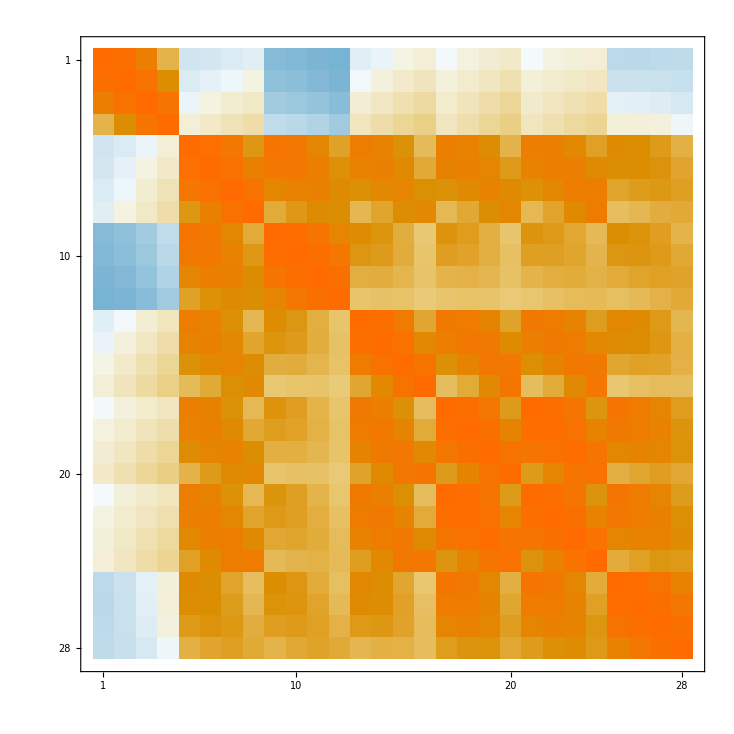

```mathematica
corr[v3]  // MatrixPlot
```